```mathematica
Needs["VectorAnalysis`"];
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
a=1;v=1;
```

```mathematica
ϕ[x_,y_]:=-v*Cos[t]*(r+a^3/(2 r^2))/.t->ArcTan[x,y]/.r->√(x^2+y^2);
```

```mathematica
vx[x_,y_]:=Grad[ϕ[Xx,Yy]][[1]]/.Xx->x/.Yy->y;
vy[x_,y_]:=Grad[ϕ[Xx,Yy]][[2]]/.Xx->x/.Yy->y;
```

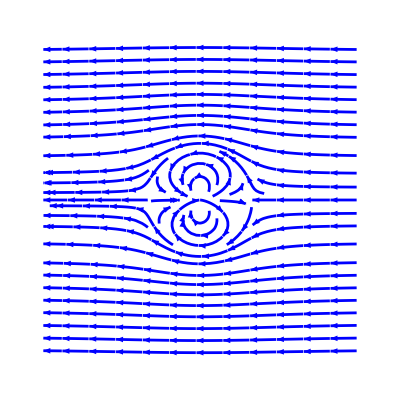

```mathematica
sp=StreamPlot[{vx[x,y],vy[x,y]},{x,-3,3},{y,-3,3},Frame->False,StreamStyle->Directive[Thickness[0.005],Blue]]
```

```mathematica
ball=Graphics[{EdgeForm[Thick], White,Disk[{0,0},1]}]
```

-Graphics-

```mathematica
Export["~/dc/fizega/camp10/em/pics/fluid_lines.pdf",Show[{sp,ball}]]
```

~/dc/fizega/camp10/em/pics/fluid_lines.pdf

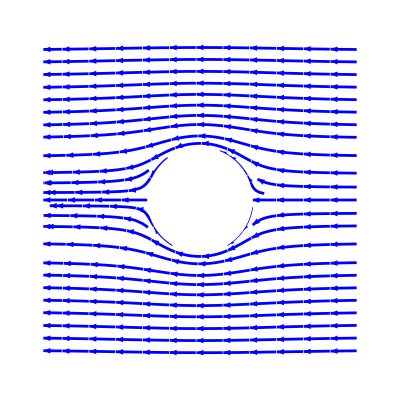

```mathematica
Show[{sp,ball}]
```

```mathematica
??StreamStyle
```

StreamStyle is an option to StreamPlot, StreamDensityPlot and related functions that determines the style to use for drawing streamlines.

Attributes[StreamStyle]={Protected}